# Comparison of DMS immune escape to MLR growth advantage

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/ncov-escape/escape-mlr-comparison

## Colors

```mathematica
toHexString[n_Integer]:=StringJoin[ToString/@(IntegerDigits[n,16]/.Thread[Range[10,15]->CharacterRange["A","F"]])]
```

```mathematica
rgbColorToHex[rgbColor_]:="#"<>StringJoin[Map[toHexString[Round[#*255]]&,Level[rgbColor,1]]]
```

```mathematica
start[n_]:=0.07;
```

```mathematica
stop[n_]:=0.99;
```

```mathematica
gap[n_]:=(stop[n]-start[n])/(n-1)
```

```mathematica
makeColors[n_]:=Table[ColorData["Rainbow"][i],{i,start[n],stop[n],gap[n]}];
```

```mathematica
colors=Append[makeColors[6],Gray]
```

{RGBColor[0.30382016, 0.13051672, 0.67703096],RGBColor[0.26866900800000004, 0.492994304, 0.7985057680000001],RGBColor[0.4305106, 0.702073568, 0.5395238880000001],RGBColor[0.7003634240000002, 0.742645096, 0.30201920799999993],RGBColor[0.897113792, 0.5919722799999999, 0.218624288],RGBColor[0.86067868, 0.15704232000000004, 0.13666448],GrayLevel[0.5]}

```mathematica
legendPanel=SwatchLegend[colors,{"BA.2","BA.4","BA.5","BA.2.75","BQ.1","XBB","other"},LegendMarkerSize->11,LegendLayout->{"Column",1},Spacings->{0,1}]
```

```mathematica
colorRamp[t_]:=Blend[{GrayLevel[0.99],Lighter[ColorData["Rainbow"][0.75],0.4],Lighter[ColorData["Rainbow"][0.75],0.05],RGBColor[0.5807,0.6182,0.4944],Darker[ColorData["Rainbow"][0.3],0.05],Darker[ColorData["Rainbow"][0.3],0.4],GrayLevel[0.05]},t]
```

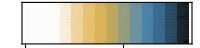

```mathematica
gaPanel=Rotate[DensityPlot[(x-0.5)/2,{x,0,2.5},{y,0,1},ColorFunction->colorRamp,ColorFunctionScaling->False,AspectRatio->0.1,PlotRangePadding->0,FrameTicks->{{None,None},{Automatic,None}}, ImageSize->200],Pi/2]
```

## Immune escape

```mathematica
escape=Import["../escape-score/escape_scores.tsv","TSV"];
```

```mathematica
escapeHeader=escape[[1]]
```

{seqName,clade,Nextclade_pango,partiallyAliased,immune_escape,ace2_binding}

```mathematica
escapeHeaderRules=MapIndexed[#1->#2[[1]]&,escapeHeader]
```

{seqName→1,clade→2,Nextclade_pango→3,partiallyAliased→4,immune_escape→5,ace2_binding→6}

```mathematica
escape=Drop[escape,1];
```

```mathematica
escape=DeleteCases[escape,x_/;x[[2]]=="outgroup"];
```

```mathematica
Length[escape]
```

496

```mathematica
TableForm[escape,TableHeadings->{None,escapeHeader}]
```

seqName | clade | Nextclade_pango | partiallyAliased | immune_escape | ace2_binding
BA.2 | 21L (Omicron) | BA.2 | BA.2 | 0 | 0
XBA | recombinant | XBA | XBA | 0.315502 | 0.20216
XAV | recombinant | XAV | XAV | 0.386325 | 0.55831
XAN | recombinant | XAN | XAN | 0.386325 | 0.55831
XBD | recombinant | XBD | XBD | 0.633879 | 0.4677
XAJ | recombinant | XAJ | XAJ | 0.386325 | 0.35483
XAZ | recombinant | XAZ | XAZ | 0.386325 | 0.55831
XAS | recombinant | XAS | XAS | 0.386325 | 0.55831
XAY | recombinant | XAY | XAY | 0.528346 | 0.61445
XAY.1 | recombinant | XAY.1 | XAY.1 | 0.528346 | 0.61445
XAY.2 | recombinant | XAY.2 | XAY.2 | 0.528346 | 0.61445
XBC | recombinant | XBC | XBC | 0.326298 | 0.68716
XBC.2 | recombinant | XBC.2 | XBC.2 | 0.326298 | 0.68716
XBC.1 | recombinant | XBC.1 | XBC.1 | 0.528346 | 0.79272
XBB | 22F (Omicron) | XBB | XBB | 0.907001 | 0.40687
XBB.5 | 22F (Omicron) | XBB.5 | XBB.5 | 0.907001 | 0.40687
XBB.2 | 22F (Omicron) | XBB.2 | XBB.2 | 0.907001 | 0.40687
XBB.4 | 22F (Omicron) | XBB.4 | XBB.4 | 0.979915 | 0.30641
XBB.3 | 22F (Omicron) | XBB.3 | XBB.3 | 0.907001 | 0.40687
XBB.3.1 | 22F (Omicron) | XBB.3.1 | XBB.3.1 | 0.907001 | 0.40687
XBB.1 | 22F (Omicron) | XBB.1 | XBB.1 | 0.907001 | 0.40687
XBB.1.1 | 22F (Omicron) | XBB.1.1 | XBB.1.1 | 0.907001 | 0.40687
XBB.1.2 | 22F (Omicron) | XBB.1.2 | XBB.1.2 | 0.907001 | 0.40687
XBB.1.3 | 22F (Omicron) | XBB.1.3 | XBB.1.3 | 0.983269 | 0.49564
BA.2.16 | 21L (Omicron) | BA.2.16 | BA.2.16 | -0.000089996 | 0
BA.2.15 | 21L (Omicron) | BA.2.15 | BA.2.15 | -0.000089996 | 0
BA.2.19 | 21L (Omicron) | BA.2.19 | BA.2.19 | -0.000089996 | 0
BA.2.1 | 21L (Omicron) | BA.2.1 | BA.2.1 | -0.000089996 | 0
BA.2.11 | 21L (Omicron) | BA.2.11 | BA.2.11 | 0.171804 | -0.04096
BA.2.18 | 21L (Omicron) | BA.2.18 | BA.2.18 | 0.047316 | 0.23107
BA.2.20 | 21L (Omicron) | BA.2.20 | BA.2.20 | -0.000089996 | 0
BA.2.24 | 21L (Omicron) | BA.2.24 | BA.2.24 | 0.0131085 | -0.03172
BA.2.26 | 21L (Omicron) | BA.2.26 | BA.2.26 | -0.000089996 | 0
BA.2.27 | 21L (Omicron) | BA.2.27 | BA.2.27 | -0.000089996 | 0
BA.2.28 | 21L (Omicron) | BA.2.28 | BA.2.28 | -0.000089996 | 0
BA.2.29 | 21L (Omicron) | BA.2.29 | BA.2.29 | -0.000089996 | 0
BA.2.30 | 21L (Omicron) | BA.2.30 | BA.2.30 | -0.000089996 | 0
BA.2.32 | 21L (Omicron) | BA.2.32 | BA.2.32 | -0.000089996 | 0
BA.2.4 | 21L (Omicron) | BA.2.4 | BA.2.4 | -0.000089996 | 0
BA.2.39 | 21L (Omicron) | BA.2.39 | BA.2.39 | -0.000089996 | 0
BA.2.41 | 21L (Omicron) | BA.2.41 | BA.2.41 | -0.000089996 | 0
BA.2.43 | 21L (Omicron) | BA.2.43 | BA.2.43 | 0.017546 | 0.11285
BA.2.42 | 21L (Omicron) | BA.2.42 | BA.2.42 | -0.000089996 | 0
BA.2.46 | 21L (Omicron) | BA.2.46 | BA.2.46 | -0.000089996 | 0
BA.2.48 | 21L (Omicron) | BA.2.48 | BA.2.48 | -0.000089996 | 0
BA.2.5 | 21L (Omicron) | BA.2.5 | BA.2.5 | -0.000089996 | 0
BA.2.55 | 21L (Omicron) | BA.2.55 | BA.2.55 | -0.000089996 | 0
BA.2.54 | 21L (Omicron) | BA.2.54 | BA.2.54 | -0.000089996 | 0
BA.2.58 | 21L (Omicron) | BA.2.58 | BA.2.58 | -0.000089996 | 0
BA.2.59 | 21L (Omicron) | BA.2.59 | BA.2.59 | -0.000089996 | 0
BA.2.60 | 21L (Omicron) | BA.2.60 | BA.2.60 | -0.000089996 | 0
BA.2.62 | 21L (Omicron) | BA.2.62 | BA.2.62 | -0.000089996 | 0
BA.2.61 | 21L (Omicron) | BA.2.61 | BA.2.61 | -0.000089996 | 0
BA.2.63 | 21L (Omicron) | BA.2.63 | BA.2.63 | -0.000089996 | 0
BA.2.65 | 21L (Omicron) | BA.2.65 | BA.2.65 | -0.000089996 | 0
BA.2.64 | 21L (Omicron) | BA.2.64 | BA.2.64 | -0.000089996 | 0
BA.2.70 | 21L (Omicron) | BA.2.70 | BA.2.70 | -0.000089996 | 0
BA.2.77 | 21L (Omicron) | BA.2.77 | BA.2.77 | 0.380024 | 0.92132
BA.2.8 | 21L (Omicron) | BA.2.8 | BA.2.8 | -0.000089996 | 0
BA.2.82 | 21L (Omicron) | BA.2.82 | BA.2.82 | 0.215487 | 0.11142
BA.2.83 | 21L (Omicron) | BA.2.83 | BA.2.83 | 0.179303 | 1.12534
BA.2.85 | 21L (Omicron) | BA.2.85 | BA.2.85 | -0.000089996 | 0
BA.2.2.1 | 21L (Omicron) | BA.2.2.1 | BA.2.2.1 | -0.000089996 | 0
BA.2.2 | 21L (Omicron) | BA.2.2 | BA.2.2 | -0.000089996 | 0
BA.2.23.1 | 21L (Omicron) | BA.2.23.1 | BA.2.23.1 | -0.000089996 | 0
BA.2.23 | 21L (Omicron) | BA.2.23 | BA.2.23 | -0.000089996 | 0
BA.2.31 | 21L (Omicron) | BA.2.31 | BA.2.31 | -0.000089996 | 0
BA.2.31.1 | 21L (Omicron) | BA.2.31.1 | BA.2.31.1 | -0.000089996 | 0
BA.2.33 | 21L (Omicron) | BA.2.33 | BA.2.33 | -0.000089996 | 0
BA.2.35 | 21L (Omicron) | BA.2.35 | BA.2.35 | 0.171804 | -0.04096
BA.2.40.1 | 21L (Omicron) | BA.2.40.1 | BA.2.40.1 | 0.047316 | 0.23107
BA.2.40 | 21L (Omicron) | BA.2.40 | BA.2.40 | -0.000089996 | 0
BA.2.49 | 21L (Omicron) | BA.2.49 | BA.2.49 | -0.000089996 | 0
BA.2.50 | 21L (Omicron) | BA.2.50 | BA.2.50 | -0.000089996 | 0
BA.2.56 | 21L (Omicron) | BA.2.56 | BA.2.56 | 0.171804 | 0.10556
BA.2.56.1 | 21L (Omicron) | BA.2.56.1 | BA.2.56.1 | 0.171804 | 0.10556
BA.2.10 | 21L (Omicron) | BA.2.10 | BA.2.10 | -0.000089996 | 0
BA.2.10.2 | 21L (Omicron) | BA.2.10.2 | BA.2.10.2 | -0.000089996 | 0
BA.2.10.3 | 21L (Omicron) | BA.2.10.3 | BA.2.10.3 | -0.000089996 | 0
BA.2.10.4 | 21L (Omicron) | BA.2.10.4 | BA.2.10.4 | 0.362464 | 0.73328
BA.2.10.1 | 21L (Omicron) | BA.2.10.1 | BA.2.10.1 | -0.000089996 | 0
BJ.1 | 21L (Omicron) | BJ.1 | BA.2.10.1.1 | 0.571427 | 0.09519
BA.2.14 | 21L (Omicron) | BA.2.14 | BA.2.14 | -0.000089996 | 0
BA.2.22 | 21L (Omicron) | BA.2.22 | BA.2.22 | -0.000089996 | 0
BA.2.34 | 21L (Omicron) | BA.2.34 | BA.2.34 | -0.000089996 | 0
BA.2.36 | 21L (Omicron) | BA.2.36 | BA.2.36 | -0.000089996 | 0
BA.2.47 | 21L (Omicron) | BA.2.47 | BA.2.47 | -0.000089996 | 0
BA.2.45 | 21L (Omicron) | BA.2.45 | BA.2.45 | 0.0675245 | -0.30756
BA.2.51 | 21L (Omicron) | BA.2.51 | BA.2.51 | -0.000089996 | 0
BA.2.53 | 21L (Omicron) | BA.2.53 | BA.2.53 | 0.0675245 | -0.33553
BA.2.52 | 21L (Omicron) | BA.2.52 | BA.2.52 | -0.000089996 | 0
BA.2.6 | 21L (Omicron) | BA.2.6 | BA.2.6 | -0.000089996 | 0
BA.2.7 | 21L (Omicron) | BA.2.7 | BA.2.7 | -0.000089996 | 0
BA.2.69 | 21L (Omicron) | BA.2.69 | BA.2.69 | -0.000089996 | 0
BA.2.71 | 21L (Omicron) | BA.2.71 | BA.2.71 | -0.000089996 | 0
BA.2.72 | 21L (Omicron) | BA.2.72 | BA.2.72 | -0.000089996 | 0
BA.2.81 | 21L (Omicron) | BA.2.81 | BA.2.81 | 0.171804 | 0.10556
BA.2.80 | 21L (Omicron) | BA.2.80 | BA.2.80 | 0.37993 | 0.10838
BA.2.25 | 21L (Omicron) | BA.2.25 | BA.2.25 | -0.000089996 | 0
BA.2.25.1 | 21L (Omicron) | BA.2.25.1 | BA.2.25.1 | -0.000089996 | 0
BA.2.44 | 21L (Omicron) | BA.2.44 | BA.2.44 | 0.017546 | 0.11285
BA.2.13 | 21L (Omicron) | BA.2.13 | BA.2.13 | 0.171804 | 0.10556
BA.2.13.1 | 21L (Omicron) | BA.2.13.1 | BA.2.13.1 | 0.171804 | 0.10556
BA.2.9 | 21L (Omicron) | BA.2.9 | BA.2.9 | -0.000089996 | 0
BA.2.9.2 | 21L (Omicron) | BA.2.9.2 | BA.2.9.2 | -0.000089996 | 0
BA.2.9.3 | 21L (Omicron) | BA.2.9.3 | BA.2.9.3 | -0.000089996 | 0
BA.2.9.1 | 21L (Omicron) | BA.2.9.1 | BA.2.9.1 | 0.171804 | 0.10556
BA.2.9.4 | 21L (Omicron) | BA.2.9.4 | BA.2.9.4 | 0.215487 | 0.11142
BA.2.9.5 | 21L (Omicron) | BA.2.9.5 | BA.2.9.5 | -0.000089996 | 0
BA.2.9.6 | 21L (Omicron) | BA.2.9.6 | BA.2.9.6 | 0.171804 | 0.10556
BA.2.3.10 | 21L (Omicron) | BA.2.3.10 | BA.2.3.10 | -0.000089996 | 0
BA.2.3.1 | 21L (Omicron) | BA.2.3.1 | BA.2.3.1 | -0.000089996 | 0
BA.2.3 | 21L (Omicron) | BA.2.3 | BA.2.3 | -0.000089996 | 0
BA.2.3.12 | 21L (Omicron) | BA.2.3.12 | BA.2.3.12 | -0.000089996 | 0
BA.2.3.13 | 21L (Omicron) | BA.2.3.13 | BA.2.3.13 | -0.000089996 | 0
BA.2.3.11 | 21L (Omicron) | BA.2.3.11 | BA.2.3.11 | -0.000089996 | 0
BA.2.3.14 | 21L (Omicron) | BA.2.3.14 | BA.2.3.14 | -0.000089996 | 0
BA.2.3.15 | 21L (Omicron) | BA.2.3.15 | BA.2.3.15 | -0.000089996 | 0
BA.2.3.17 | 21L (Omicron) | BA.2.3.17 | BA.2.3.17 | -0.000089996 | 0
BA.2.3.18 | 21L (Omicron) | BA.2.3.18 | BA.2.3.18 | -0.000089996 | 0
BA.2.3.19 | 21L (Omicron) | BA.2.3.19 | BA.2.3.19 | 0.047316 | 0.23107
BA.2.3.21 | 21L (Omicron) | BA.2.3.21 | BA.2.3.21 | 0.0197094 | 1.06758
BA.2.3.4 | 21L (Omicron) | BA.2.3.4 | BA.2.3.4 | -0.000089996 | 0
BA.2.3.5 | 21L (Omicron) | BA.2.3.5 | BA.2.3.5 | -0.000089996 | 0
BA.2.3.7 | 21L (Omicron) | BA.2.3.7 | BA.2.3.7 | -0.000089996 | 0
BA.2.3.6 | 21L (Omicron) | BA.2.3.6 | BA.2.3.6 | -0.000089996 | 0
BA.2.3.8 | 21L (Omicron) | BA.2.3.8 | BA.2.3.8 | -0.000089996 | 0
BA.2.3.9 | 21L (Omicron) | BA.2.3.9 | BA.2.3.9 | -0.000089996 | 0
BA.2.3.16 | 21L (Omicron) | BA.2.3.16 | BA.2.3.16 | -0.000089996 | 0
BP.1 | 21L (Omicron) | BP.1 | BA.2.3.16.1 | 0.366094 | 0.94569
BA.2.3.2 | 21L (Omicron) | BA.2.3.2 | BA.2.3.2 | -0.000089996 | 0
BS.1 | 21L (Omicron) | BS.1 | BA.2.3.2.1 | 0.467909 | 0.66194
BS.1.1 | 21L (Omicron) | BS.1.1 | BA.2.3.2.1.1 | 0.636953 | 0.6589
BA.2.3.20 | 21L (Omicron) | BA.2.3.20 | BA.2.3.20 | 0.592504 | 1.06344
CM.6 | 21L (Omicron) | CM.6 | BA.2.3.20.6 | 0.592504 | 1.06344
CM.1 | 21L (Omicron) | CM.1 | BA.2.3.20.1 | 0.592504 | 1.06344
CM.4 | 21L (Omicron) | CM.4 | BA.2.3.20.4 | 0.592504 | 1.06344
CM.5 | 21L (Omicron) | CM.5 | BA.2.3.20.5 | 0.592504 | 1.06344
CM.2 | 21L (Omicron) | CM.2 | BA.2.3.20.2 | 0.592504 | 1.06344
CM.3 | 21L (Omicron) | CM.3 | BA.2.3.20.3 | 0.656153 | 0.29833
BA.2.17 | 21L (Omicron) | BA.2.17 | BA.2.17 | -0.000089996 | 0
BA.2.21 | 21L (Omicron) | BA.2.21 | BA.2.21 | -0.000089996 | 0
BA.2.37 | 21L (Omicron) | BA.2.37 | BA.2.37 | -0.000089996 | 0
BA.2.57 | 21L (Omicron) | BA.2.57 | BA.2.57 | -0.000089996 | 0
BA.2.66 | 21L (Omicron) | BA.2.66 | BA.2.66 | -0.000089996 | 0
BA.2.68 | 21L (Omicron) | BA.2.68 | BA.2.68 | -0.000089996 | 0
BA.2.74 | 21L (Omicron) | BA.2.74 | BA.2.74 | 0.347546 | 0.21698
BA.2.73 | 21L (Omicron) | BA.2.73 | BA.2.73 | -0.000089996 | 0
BA.2.78 | 21L (Omicron) | BA.2.78 | BA.2.78 | 0.171804 | 0.10556
BA.2.67 | 21L (Omicron) | BA.2.67 | BA.2.67 | -0.000089996 | 0
BA.2.79 | 21L (Omicron) | BA.2.79 | BA.2.79 | 0.152394 | -0.05858
BA.2.79.1 | 21L (Omicron) | BA.2.79.1 | BA.2.79.1 | 0.152394 | -0.05858
BA.2.76 | 21L (Omicron) | BA.2.76 | BA.2.76 | 0.215487 | 0.11142
BA.2.76.1 | 21L (Omicron) | BA.2.76.1 | BA.2.76.1 | 0.280001 | 0.18492
BA.2.76.2 | 21L (Omicron) | BA.2.76.2 | BA.2.76.2 | 0.215487 | 0.11142
BA.2.38 | 21L (Omicron) | BA.2.38 | BA.2.38 | 0.047316 | 0.23107
BA.2.38.3 | 21L (Omicron) | BA.2.38.3 | BA.2.38.3 | 0.0504432 | 0.08446
BH.1 | 21L (Omicron) | BH.1 | BA.2.38.3.1 | 0.352981 | -0.11188
BA.2.38.1 | 21L (Omicron) | BA.2.38.1 | BA.2.38.1 | 0.2264 | 0.07569
BA.2.38.2 | 21L (Omicron) | BA.2.38.2 | BA.2.38.2 | 0.2264 | 0.07569
BA.2.38.4 | 21L (Omicron) | BA.2.38.4 | BA.2.38.4 | 0.2264 | 0.07569
BA.2.12 | 21L (Omicron) | BA.2.12 | BA.2.12 | -0.000089996 | 0
BA.2.12.2 | 21L (Omicron) | BA.2.12.2 | BA.2.12.2 | 0.0606645 | 0.0735
BA.2.12.1 | 22C (Omicron) | BA.2.12.1 | BA.2.12.1 | 0.171804 | -0.12693
BG.3 | 22C (Omicron) | BG.3 | BA.2.12.1.3 | 0.171804 | -0.12693
BG.1 | 22C (Omicron) | BG.1 | BA.2.12.1.1 | 0.171804 | -0.12693
BG.2 | 22C (Omicron) | BG.2 | BA.2.12.1.2 | 0.171804 | -0.12693
BG.5 | 22C (Omicron) | BG.5 | BA.2.12.1.5 | 0.171804 | -0.12693
BG.6 | 22C (Omicron) | BG.6 | BA.2.12.1.6 | 0.171804 | -0.12693
BG.4 | 22C (Omicron) | BG.4 | BA.2.12.1.4 | 0.171804 | -0.12693
BG.7 | 22C (Omicron) | BG.7 | BA.2.12.1.7 | 0.171804 | -0.12693
22C | 22C (Omicron) | BA.2.12.1 | BA.2.12.1 | ? | ?
BA.2.75 | 22D (Omicron) | BA.2.75 | BA.2.75 | 0.191267 | 1.17547
BA.2.75.10 | 22D (Omicron) | BA.2.75.10 | BA.2.75.10 | 0.191267 | 1.17547
BA.2.75.7 | 22D (Omicron) | BA.2.75.7 | BA.2.75.7 | 0.375206 | 0.35628
BA.2.75.8 | 22D (Omicron) | BA.2.75.8 | BA.2.75.8 | 0.364485 | 1.04854
BA.2.75.9 | 22D (Omicron) | BA.2.75.9 | BA.2.75.9 | 0.405495 | 1.28689
CB.1 | 22D (Omicron) | CB.1 | BA.2.75.9.1 | 0.633879 | 0.81858
BA.2.75.4 | 22D (Omicron) | BA.2.75.4 | BA.2.75.4 | 0.364485 | 1.13451
BR.2 | 22D (Omicron) | BR.2 | BA.2.75.4.2 | 0.805266 | 0.74721
BR.3 | 22D (Omicron) | BR.3 | BA.2.75.4.3 | 0.541151 | 1.24593
BR.4 | 22D (Omicron) | BR.4 | BA.2.75.4.4 | 0.411534 | 1.10514
BR.1 | 22D (Omicron) | BR.1 | BA.2.75.4.1 | 0.460933 | 0.94495
BR.1.2 | 22D (Omicron) | BR.1.2 | BA.2.75.4.1.2 | 0.706243 | 0.12576
BR.1.1 | 22D (Omicron) | BR.1.1 | BA.2.75.4.1.1 | 0.460933 | 0.94495
BA2754 | 22D (Omicron) | BA.2.75.4 | BA.2.75.4 | ? | ?
BA.2.75.1 | 22D (Omicron) | BA.2.75.1 | BA.2.75.1 | 0.191267 | 1.17547
BL.4 | 22D (Omicron) | BL.4 | BA.2.75.1.4 | 0.191267 | 1.17547
BL.3 | 22D (Omicron) | BL.3 | BA.2.75.1.3 | 0.191267 | 1.17547
BL.2 | 22D (Omicron) | BL.2 | BA.2.75.1.2 | 0.405495 | 1.28689
BL.2.1 | 22D (Omicron) | BL.2.1 | BA.2.75.1.2.1 | 0.405495 | 1.28689
22612T | 22D (Omicron) | BA.2.75.1 | BA.2.75.1 | ? | ?
BL.1.1 | 22D (Omicron) | BL.1.1 | BA.2.75.1.1.1 | 0.405495 | 1.28689
BL.1.2 | 22D (Omicron) | BL.1.2 | BA.2.75.1.1.2 | 0.405495 | 1.28689
BL.1 | 22D (Omicron) | BL.1 | BA.2.75.1.1 | 0.405495 | 1.28689
BL.1.4 | 22D (Omicron) | BL.1.4 | BA.2.75.1.1.4 | 0.571451 | 1.34644
BL.1.3 | 22D (Omicron) | BL.1.3 | BA.2.75.1.1.3 | 0.571451 | 1.19193
BA.2.75.6 | 22D (Omicron) | BA.2.75.6 | BA.2.75.6 | 0.405495 | 1.28689
BY.1 | 22D (Omicron) | BY.1 | BA.2.75.6.1 | 0.633879 | 0.4677
BY.1.1.1 | 22D (Omicron) | BY.1.1.1 | BA.2.75.6.1.1.1 | 0.805266 | 0.42674
BY.1.1 | 22D (Omicron) | BY.1.1 | BA.2.75.6.1.1 | 0.805266 | 0.42674
BY.1.2 | 22D (Omicron) | BY.1.2 | BA.2.75.6.1.2 | 0.633879 | 0.4677
BY.1.2.1 | 22D (Omicron) | BY.1.2.1 | BA.2.75.6.1.2.1 | 0.670085 | 0.41647
BA.2.75.2 | 22D (Omicron) | BA.2.75.2 | BA.2.75.2 | 0.633879 | 0.4677
CA.1 | 22D (Omicron) | CA.1 | BA.2.75.2.1 | 0.805266 | 0.42674
CA.2 | 22D (Omicron) | CA.2 | BA.2.75.2.2 | 0.670085 | 0.41647
CA.3 | 22D (Omicron) | CA.3 | BA.2.75.2.3 | 0.633879 | 0.4677
CA.5 | 22D (Omicron) | CA.5 | BA.2.75.2.5 | 0.633879 | 0.4677
CA.4 | 22D (Omicron) | CA.4 | BA.2.75.2.4 | 0.633879 | 1.07323
CA.6 | 22D (Omicron) | CA.6 | BA.2.75.2.6 | 0.633879 | 0.4677
CA.7 | 22D (Omicron) | CA.7 | BA.2.75.2.7 | 0.805266 | 0.42674
BA.2.75.5 | 22D (Omicron) | BA.2.75.5 | BA.2.75.5 | 0.400563 | 1.17243
BN.4 | 22D (Omicron) | BN.4 | BA.2.75.5.4 | 0.563728 | 1.14197
BN.6 | 22D (Omicron) | BN.6 | BA.2.75.5.6 | 0.400563 | 1.17243
BN.5 | 22D (Omicron) | BN.5 | BA.2.75.5.5 | 0.400563 | 1.17243
BN.2.1 | 22D (Omicron) | BN.2.1 | BA.2.75.5.2.1 | 0.563728 | 1.14197
BN.2 | 22D (Omicron) | BN.2 | BA.2.75.5.2 | 0.400563 | 1.17243
BN.3 | 22D (Omicron) | BN.3 | BA.2.75.5.3 | 0.540142 | 1.11385
BN.3.1 | 22D (Omicron) | BN.3.1 | BA.2.75.5.3.1 | 0.687477 | 1.08339
BN.1 | 22D (Omicron) | BN.1 | BA.2.75.5.1 | 0.76074 | 1.25339
BN.1.3 | 22D (Omicron) | BN.1.3 | BA.2.75.5.1.3 | 0.76074 | 1.25339
BN.1.5 | 22D (Omicron) | BN.1.5 | BA.2.75.5.1.5 | 0.76074 | 1.25339
BN.1.4 | 22D (Omicron) | BN.1.4 | BA.2.75.5.1.4 | 0.76074 | 1.25339
BN.1.6 | 22D (Omicron) | BN.1.6 | BA.2.75.5.1.6 | 0.76074 | 1.25339
BN.1.1 | 22D (Omicron) | BN.1.1 | BA.2.75.5.1.1 | 0.779859 | 1.20216
BN.1.1.1 | 22D (Omicron) | BN.1.1.1 | BA.2.75.5.1.1.1 | 0.779859 | 1.20216
BN.1.2.1 | 22D (Omicron) | BN.1.2.1 | BA.2.75.5.1.2.1 | 0.787005 | 1.21326
BN.1.2 | 22D (Omicron) | BN.1.2 | BA.2.75.5.1.2 | 0.76074 | 1.25339
BA.2.75.3 | 22D (Omicron) | BA.2.75.3 | BA.2.75.3 | 0.191267 | 1.17547
BM.3 | 22D (Omicron) | BM.3 | BA.2.75.3.3 | 0.191267 | 1.17547
BM.5 | 22D (Omicron) | BM.5 | BA.2.75.3.5 | 0.235074 | 1.15852
BM.6 | 22D (Omicron) | BM.6 | BA.2.75.3.6 | 0.235074 | 1.15852
BM.2 | 22D (Omicron) | BM.2 | BA.2.75.3.2 | 0.405495 | 1.28689
BM.2.2 | 22D (Omicron) | BM.2.2 | BA.2.75.3.2.2 | 0.457328 | 1.26994
BM.2.1 | 22D (Omicron) | BM.2.1 | BA.2.75.3.2.1 | 0.633879 | 0.81858
BM.2.3 | 22D (Omicron) | BM.2.3 | BA.2.75.3.2.3 | 0.633879 | 0.78817
BM.4 | 22D (Omicron) | BM.4 | BA.2.75.3.4 | 0.191267 | 1.17547
BM.4.1 | 22D (Omicron) | BM.4.1 | BA.2.75.3.4.1 | 0.375206 | 0.35628
BM.4.1.1 | 22D (Omicron) | BM.4.1.1 | BA.2.75.3.4.1.1 | 0.633879 | 0.4677
CH.2 | 22D (Omicron) | CH.2 | BA.2.75.3.4.1.1.2 | 0.633879 | 0.4677
CH.1 | 22D (Omicron) | CH.1 | BA.2.75.3.4.1.1.1 | 0.737592 | 0.36892
CH.1.1 | 22D (Omicron) | CH.1.1 | BA.2.75.3.4.1.1.1.1 | 0.906805 | 0.32796
BM.1 | 22D (Omicron) | BM.1 | BA.2.75.3.1 | 0.375206 | 0.35628
BM.1.1.2 | 22D (Omicron) | BM.1.1.2 | BA.2.75.3.1.1.2 | 0.633879 | 0.4677
BM.1.1 | 22D (Omicron) | BM.1.1 | BA.2.75.3.1.1 | 0.633879 | 0.4677
BM.1.1.1 | 22D (Omicron) | BM.1.1.1 | BA.2.75.3.1.1.1 | 0.836642 | 0.43724
CJ.1 | 22D (Omicron) | CJ.1 | BA.2.75.3.1.1.1.1 | 0.836642 | 1.04277
BM.1.1.3 | 22D (Omicron) | BM.1.1.3 | BA.2.75.3.1.1.3 | 0.633879 | 0.4677
CV.1 | 22D (Omicron) | CV.1 | BA.2.75.3.1.1.3.1 | 0.805266 | 0.42674
BA.4.8 | 22A (Omicron) | BA.4.8 | BA.4.8 | 0.386325 | 0.55831
BA.4 | 22A (Omicron) | BA.4 | BA.4 | 0.386325 | 0.55831
BA.4.2 | 22A (Omicron) | BA.4.2 | BA.4.2 | 0.386325 | 0.55831
BA.4.3 | 22A (Omicron) | BA.4.3 | BA.4.3 | 0.386325 | 0.55831
BA.4.5 | 22A (Omicron) | BA.4.5 | BA.4.5 | 0.386325 | 0.55831
BA.4.4 | 22A (Omicron) | BA.4.4 | BA.4.4 | 0.386325 | 0.55831
BA.4.7 | 22A (Omicron) | BA.4.7 | BA.4.7 | 0.601423 | 0.55138
BA.4.6 | 22A (Omicron) | BA.4.6 | BA.4.6 | 0.601423 | 0.66973
BA.4.6.1 | 22A (Omicron) | BA.4.6.1 | BA.4.6.1 | 0.601423 | 0.66973
BA.4.6.2 | 22A (Omicron) | BA.4.6.2 | BA.4.6.2 | 0.736094 | 0.50263
BA.4.6.3 | 22A (Omicron) | BA.4.6.3 | BA.4.6.3 | 0.831378 | 0.71883
BA.4.6.4 | 22A (Omicron) | BA.4.6.4 | BA.4.6.4 | 0.601423 | 0.66973
BA.4.1.1 | 22A (Omicron) | BA.4.1.1 | BA.4.1.1 | 0.386325 | 0.55831
BA.4.1 | 22A (Omicron) | BA.4.1 | BA.4.1 | 0.386325 | 0.55831
BA.4.1.4 | 22A (Omicron) | BA.4.1.4 | BA.4.1.4 | 0.386325 | 0.55831
BA.4.1.3 | 22A (Omicron) | BA.4.1.3 | BA.4.1.3 | 0.386325 | 0.55831
BA.4.1.6 | 22A (Omicron) | BA.4.1.6 | BA.4.1.6 | 0.386325 | 0.55831
BA.4.1.5 | 22A (Omicron) | BA.4.1.5 | BA.4.1.5 | 0.386325 | 0.55831
BA.4.1.8 | 22A (Omicron) | BA.4.1.8 | BA.4.1.8 | 0.601423 | 0.66973
BA.4.1.9 | 22A (Omicron) | BA.4.1.9 | BA.4.1.9 | 0.601423 | 0.66973
BA.4.1.2 | 22A (Omicron) | BA.4.1.2 | BA.4.1.2 | 0.386325 | 0.55831
BA.4.1.7 | 22A (Omicron) | BA.4.1.7 | BA.4.1.7 | 0.386325 | 0.55831
BA.4.1.10 | 22A (Omicron) | BA.4.1.10 | BA.4.1.10 | 0.659469 | 0.67074
CS.1 | 22A (Omicron) | CS.1 | BA.4.1.10.1 | 0.845774 | 0.57028
BA.5 | 22B (Omicron) | BA.5 | BA.5 | 0.386325 | 0.55831
BA.5.9 | 22B (Omicron) | BA.5.9 | BA.5.9 | 0.601423 | 0.39901
BA.5.7 | 22B (Omicron) | BA.5.7 | BA.5.7 | 0.386325 | 0.55831
BA.5.8 | 22B (Omicron) | BA.5.8 | BA.5.8 | 0.386325 | 0.55831
BA.5.5 | 22B (Omicron) | BA.5.5 | BA.5.5 | 0.386325 | 0.55831
BA.5.5.2 | 22B (Omicron) | BA.5.5.2 | BA.5.5.2 | 0.386325 | 0.55831
BA.5.5.3 | 22B (Omicron) | BA.5.5.3 | BA.5.5.3 | 0.386325 | 0.55831
BA.5.5.1 | 22B (Omicron) | BA.5.5.1 | BA.5.5.1 | 0.502672 | 0.49973
BA.5.6 | 22B (Omicron) | BA.5.6 | BA.5.6 | 0.386325 | 0.55831
BA.5.6.2 | 22B (Omicron) | BA.5.6.2 | BA.5.6.2 | 0.585925 | 0.45953
BW.1 | 22B (Omicron) | BW.1 | BA.5.6.2.1 | 0.630694 | 0.66401
BA.5.6.1 | 22B (Omicron) | BA.5.6.1 | BA.5.6.1 | 0.386325 | 0.55831
BA.5.6.3 | 22B (Omicron) | BA.5.6.3 | BA.5.6.3 | 0.601423 | 0.66973
BA.5.6.4 | 22B (Omicron) | BA.5.6.4 | BA.5.6.4 | 0.601423 | 0.58831
BA.5.1 | 22B (Omicron) | BA.5.1 | BA.5.1 | 0.386325 | 0.55831
BA.5.1.11 | 22B (Omicron) | BA.5.1.11 | BA.5.1.11 | 0.386325 | 0.55831
BA.5.1.12 | 22B (Omicron) | BA.5.1.12 | BA.5.1.12 | 0.504611 | 0.39121
BA.5.1.14 | 22B (Omicron) | BA.5.1.14 | BA.5.1.14 | 0.386325 | 0.55831
BA.5.1.15 | 22B (Omicron) | BA.5.1.15 | BA.5.1.15 | 0.386325 | 0.55831
BA.5.1.17 | 22B (Omicron) | BA.5.1.17 | BA.5.1.17 | 0.386325 | 0.55831
BA.5.1.16 | 22B (Omicron) | BA.5.1.16 | BA.5.1.16 | 0.386325 | 0.55831
BA.5.1.2 | 22B (Omicron) | BA.5.1.2 | BA.5.1.2 | 0.386325 | 0.55831
BA.5.1.24 | 22B (Omicron) | BA.5.1.24 | BA.5.1.24 | 0.386325 | 0.55831
BA.5.1.22 | 22B (Omicron) | BA.5.1.22 | BA.5.1.22 | 0.386325 | 0.55831
BA.5.1.23 | 22B (Omicron) | BA.5.1.23 | BA.5.1.23 | 0.386325 | 0.55831
BA.5.1.25 | 22B (Omicron) | BA.5.1.25 | BA.5.1.25 | 0.386325 | 0.55831
BA.5.1.3 | 22B (Omicron) | BA.5.1.3 | BA.5.1.3 | 0.386325 | 0.55831
BA.5.1.4 | 22B (Omicron) | BA.5.1.4 | BA.5.1.4 | 0.386325 | 0.55831
BA.5.1.5 | 22B (Omicron) | BA.5.1.5 | BA.5.1.5 | 0.386325 | 0.55831
BA.5.1.30 | 22B (Omicron) | BA.5.1.30 | BA.5.1.30 | 0.386325 | 0.55831
BA.5.1.28 | 22B (Omicron) | BA.5.1.28 | BA.5.1.28 | 0.601423 | 0.66973
BA.5.1.6 | 22B (Omicron) | BA.5.1.6 | BA.5.1.6 | 0.386325 | 0.55831
BA.5.1.7 | 22B (Omicron) | BA.5.1.7 | BA.5.1.7 | 0.386325 | 0.55831
BA.5.1.8 | 22B (Omicron) | BA.5.1.8 | BA.5.1.8 | 0.386325 | 0.55831
BA.5.1.10 | 22B (Omicron) | BA.5.1.10 | BA.5.1.10 | 0.386325 | 0.55831
BK.1 | 22B (Omicron) | BK.1 | BA.5.1.10.1 | 0.386325 | 0.55831
BA.5.1.26 | 22B (Omicron) | BA.5.1.26 | BA.5.1.26 | 0.601423 | 0.66973
CU.1 | 22B (Omicron) | CU.1 | BA.5.1.26.1 | 0.601423 | 0.66973
BA.5.1.27 | 22B (Omicron) | BA.5.1.27 | BA.5.1.27 | 0.601423 | 0.66973
BA.5.1.29 | 22B (Omicron) | BA.5.1.29 | BA.5.1.29 | 0.585925 | 0.40293
CL.1 | 22B (Omicron) | CL.1 | BA.5.1.29.1 | 0.630694 | 0.60741
BA.5.1.1 | 22B (Omicron) | BA.5.1.1 | BA.5.1.1 | 0.386325 | 0.55831
BA.5.1.19 | 22B (Omicron) | BA.5.1.19 | BA.5.1.19 | 0.386325 | 0.55831
BA.5.1.20 | 22B (Omicron) | BA.5.1.20 | BA.5.1.20 | 0.601423 | 0.66973
BA.5.1.9 | 22B (Omicron) | BA.5.1.9 | BA.5.1.9 | 0.386325 | 0.55831
BA.5.1.18 | 22B (Omicron) | BA.5.1.18 | BA.5.1.18 | 0.601423 | 0.66973
BA.5.1.21 | 22B (Omicron) | BA.5.1.21 | BA.5.1.21 | 0.386325 | 0.55831
BT.1 | 22B (Omicron) | BT.1 | BA.5.1.21.1 | 0.386325 | 0.55831
BT.2 | 22B (Omicron) | BT.2 | BA.5.1.21.2 | 0.386325 | 0.55831
BA.5.3 | 22B (Omicron) | BA.5.3 | BA.5.3 | 0.386325 | 0.55831
BA.5.3.3 | 22B (Omicron) | BA.5.3.3 | BA.5.3.3 | 0.386325 | 0.55831
BA.5.3.5 | 22B (Omicron) | BA.5.3.5 | BA.5.3.5 | 0.601423 | 0.66973
BA.5.3.2 | 22B (Omicron) | BA.5.3.2 | BA.5.3.2 | 0.386325 | 0.55831
BA.5.3.4 | 22B (Omicron) | BA.5.3.4 | BA.5.3.4 | 0.386325 | 0.55831
BA.5.3.1 | 22B (Omicron) | BA.5.3.1 | BA.5.3.1 | 0.386325 | 0.55831
BE.3 | 22B (Omicron) | BE.3 | BA.5.3.1.3 | 0.386325 | 0.55831
BE.2 | 22B (Omicron) | BE.2 | BA.5.3.1.2 | 0.386325 | 0.55831
BE.5 | 22B (Omicron) | BE.5 | BA.5.3.1.5 | 0.386325 | 0.55831
BE.4 | 22B (Omicron) | BE.4 | BA.5.3.1.4 | 0.386325 | 0.55831
BE.4.2 | 22B (Omicron) | BE.4.2 | BA.5.3.1.4.2 | 0.630694 | 0.60741
BE.4.1 | 22B (Omicron) | BE.4.1 | BA.5.3.1.4.1 | 0.601423 | 0.66973
BE.4.1.1 | 22B (Omicron) | BE.4.1.1 | BA.5.3.1.4.1.1 | 0.778702 | 0.56927
CQ.1 | 22B (Omicron) | CQ.1 | BA.5.3.1.4.1.1.1 | 0.778702 | 0.56927
CQ.2 | 22B (Omicron) | CQ.2 | BA.5.3.1.4.1.1.2 | 0.822067 | 0.40217
BE.1 | 22B (Omicron) | BE.1 | BA.5.3.1.1 | 0.386325 | 0.55831
BE.1.3 | 22B (Omicron) | BE.1.3 | BA.5.3.1.1.3 | 0.386325 | 0.55831
BE.1.2 | 22B (Omicron) | BE.1.2 | BA.5.3.1.1.2 | 0.601423 | 0.66973
BE.1.2.1 | 22B (Omicron) | BE.1.2.1 | BA.5.3.1.1.2.1 | 0.736094 | 0.50263
BE.1.4 | 22B (Omicron) | BE.1.4 | BA.5.3.1.1.4 | 0.386325 | 0.55831
BE.1.4.3 | 22B (Omicron) | BE.1.4.3 | BA.5.3.1.1.4.3 | 0.504611 | 0.39121
BE.1.4.4 | 22B (Omicron) | BE.1.4.4 | BA.5.3.1.1.4.4 | 0.386325 | 0.55831
BE.1.4.2 | 22B (Omicron) | BE.1.4.2 | BA.5.3.1.1.4.2 | 0.601423 | 0.66973
BE.1.4.1 | 22B (Omicron) | BE.1.4.1 | BA.5.3.1.1.4.1 | 0.386325 | 0.55831
BE.1.1 | 22B (Omicron) | BE.1.1 | BA.5.3.1.1.1 | 0.386325 | 0.55831
BE.1.1.2 | 22B (Omicron) | BE.1.1.2 | BA.5.3.1.1.1.2 | 0.386325 | 0.55831
CC.1 | 22B (Omicron) | CC.1 | BA.5.3.1.1.1.2.1 | 0.502672 | 0.49973
BE.1.1.1 | 22B (Omicron) | BE.1.1.1 | BA.5.3.1.1.1.1 | 0.585925 | 0.45953
BQ.2 | 22B (Omicron) | BQ.2 | BA.5.3.1.1.1.1.2 | 0.591983 | 0.45205
BQ.1 | 22E (Omicron) | BQ.1 | BA.5.3.1.1.1.1.1 | 0.630694 | 0.66401
BQ.1.11 | 22E (Omicron) | BQ.1.11 | BA.5.3.1.1.1.1.1.11 | 0.630694 | 0.66401
BQ.1.12 | 22E (Omicron) | BQ.1.12 | BA.5.3.1.1.1.1.1.12 | 0.630694 | 0.66401
BQ.1.13 | 22E (Omicron) | BQ.1.13 | BA.5.3.1.1.1.1.1.13 | 0.630694 | 0.66401
BQ.1.14 | 22E (Omicron) | BQ.1.14 | BA.5.3.1.1.1.1.1.14 | 0.630694 | 0.66401
BQ.1.15 | 22E (Omicron) | BQ.1.15 | BA.5.3.1.1.1.1.1.15 | 0.630694 | 0.66401
BQ.1.17 | 22E (Omicron) | BQ.1.17 | BA.5.3.1.1.1.1.1.17 | 0.630694 | 0.57323
BQ.1.19 | 22E (Omicron) | BQ.1.19 | BA.5.3.1.1.1.1.1.19 | 0.652889 | 0.61278
BQ.1.20 | 22E (Omicron) | BQ.1.20 | BA.5.3.1.1.1.1.1.20 | 0.847956 | 0.5446
BQ.1.2 | 22E (Omicron) | BQ.1.2 | BA.5.3.1.1.1.1.1.2 | 0.630694 | 0.66401
BQ.1.3 | 22E (Omicron) | BQ.1.3 | BA.5.3.1.1.1.1.1.3 | 0.630694 | 0.66401
BQ.1.5 | 22E (Omicron) | BQ.1.5 | BA.5.3.1.1.1.1.1.5 | 0.630694 | 0.66401
BQ.1.4 | 22E (Omicron) | BQ.1.4 | BA.5.3.1.1.1.1.1.4 | 0.630694 | 0.66401
BQ.1.6 | 22E (Omicron) | BQ.1.6 | BA.5.3.1.1.1.1.1.6 | 0.630694 | 0.66401
BQ.1.7 | 22E (Omicron) | BQ.1.7 | BA.5.3.1.1.1.1.1.7 | 0.630694 | 0.66401
BQ.1.9 | 22E (Omicron) | BQ.1.9 | BA.5.3.1.1.1.1.1.9 | 0.831378 | 0.77543
BQ.1.10.1 | 22E (Omicron) | BQ.1.10.1 | BA.5.3.1.1.1.1.1.10.1 | 0.630694 | 0.66401
BQ.1.10 | 22E (Omicron) | BQ.1.10 | BA.5.3.1.1.1.1.1.10 | 0.630694 | 0.66401
BQ.1.16 | 22E (Omicron) | BQ.1.16 | BA.5.3.1.1.1.1.1.16 | 0.630694 | 0.66401
BQ.1.18 | 22E (Omicron) | BQ.1.18 | BA.5.3.1.1.1.1.1.18 | 0.831378 | 0.77543
BQ.1.8 | 22E (Omicron) | BQ.1.8 | BA.5.3.1.1.1.1.1.8 | 0.630694 | 0.66401
BQ.1.8.2 | 22E (Omicron) | BQ.1.8.2 | BA.5.3.1.1.1.1.1.8.2 | 0.630694 | 0.66401
BQ.1.8.1 | 22E (Omicron) | BQ.1.8.1 | BA.5.3.1.1.1.1.1.8.1 | 0.630694 | 0.66401
BQ.1.1.1 | 22E (Omicron) | BQ.1.1.1 | BA.5.3.1.1.1.1.1.1.1 | 0.831378 | 0.77543
BQ.1.1 | 22E (Omicron) | BQ.1.1 | BA.5.3.1.1.1.1.1.1 | 0.831378 | 0.77543
BQ.1.1.10 | 22E (Omicron) | BQ.1.1.10 | BA.5.3.1.1.1.1.1.1.10 | 0.831378 | 0.77543
BQ.1.1.11 | 22E (Omicron) | BQ.1.1.11 | BA.5.3.1.1.1.1.1.1.11 | 0.854816 | 0.7242
BQ.1.1.12 | 22E (Omicron) | BQ.1.1.12 | BA.5.3.1.1.1.1.1.1.12 | 0.854816 | 0.7242
BQ.1.1.13 | 22E (Omicron) | BQ.1.1.13 | BA.5.3.1.1.1.1.1.1.13 | 0.831378 | 0.77543
BQ.1.1.2 | 22E (Omicron) | BQ.1.1.2 | BA.5.3.1.1.1.1.1.1.2 | 0.831378 | 0.77543
BQ.1.1.4 | 22E (Omicron) | BQ.1.1.4 | BA.5.3.1.1.1.1.1.1.4 | 0.831378 | 0.77543
BQ.1.1.5 | 22E (Omicron) | BQ.1.1.5 | BA.5.3.1.1.1.1.1.1.5 | 0.831378 | 0.77543
BQ.1.1.3 | 22E (Omicron) | BQ.1.1.3 | BA.5.3.1.1.1.1.1.1.3 | 0.831378 | 0.77543
BQ.1.1.8 | 22E (Omicron) | BQ.1.1.8 | BA.5.3.1.1.1.1.1.1.8 | 0.831378 | 0.77543
BQ.1.1.9 | 22E (Omicron) | BQ.1.1.9 | BA.5.3.1.1.1.1.1.1.9 | 0.831378 | 0.77543
BQ.1.1.6 | 22E (Omicron) | BQ.1.1.6 | BA.5.3.1.1.1.1.1.1.6 | 0.831378 | 0.77543
BQ.1.1.7 | 22E (Omicron) | BQ.1.1.7 | BA.5.3.1.1.1.1.1.1.7 | 0.831378 | 0.77543
BA.5.10 | 22B (Omicron) | BA.5.10 | BA.5.10 | 0.386325 | 0.55831
BA.5.10.1 | 22B (Omicron) | BA.5.10.1 | BA.5.10.1 | 0.601423 | 0.66973
BA.5.2 | 22B (Omicron) | BA.5.2 | BA.5.2 | 0.386325 | 0.55831
BA.5.2.1 | 22B (Omicron) | BA.5.2.1 | BA.5.2.1 | 0.386325 | 0.55831
BF.14 | 22B (Omicron) | BF.14 | BA.5.2.1.14 | 0.502672 | 0.49973
BF.12 | 22B (Omicron) | BF.12 | BA.5.2.1.12 | 0.386325 | 0.5279
BF.17 | 22B (Omicron) | BF.17 | BA.5.2.1.17 | 0.386325 | 0.55831
BF.18 | 22B (Omicron) | BF.18 | BA.5.2.1.18 | 0.386325 | 0.55831
BF.19 | 22B (Omicron) | BF.19 | BA.5.2.1.19 | 0.386325 | 0.55831
BF.30 | 22B (Omicron) | BF.30 | BA.5.2.1.30 | 0.601423 | 0.66973
BF.4 | 22B (Omicron) | BF.4 | BA.5.2.1.4 | 0.386325 | 0.55831
BF.6 | 22B (Omicron) | BF.6 | BA.5.2.1.6 | 0.386325 | 0.55831
BF.8 | 22B (Omicron) | BF.8 | BA.5.2.1.8 | 0.386325 | 0.55831
BF.11.1 | 22B (Omicron) | BF.11.1 | BA.5.2.1.11.1 | 0.601423 | 0.66973
BF.11 | 22B (Omicron) | BF.11 | BA.5.2.1.11 | 0.601423 | 0.66973
BF.11.4 | 22B (Omicron) | BF.11.4 | BA.5.2.1.11.4 | 0.601423 | 0.66973
BF.11.5 | 22B (Omicron) | BF.11.5 | BA.5.2.1.11.5 | 0.601423 | 0.66973
BF.11.2 | 22B (Omicron) | BF.11.2 | BA.5.2.1.11.2 | 0.601423 | 0.66973
BF.11.3 | 22B (Omicron) | BF.11.3 | BA.5.2.1.11.3 | 0.601423 | 0.66973
BF.26 | 22B (Omicron) | BF.26 | BA.5.2.1.26 | 0.386325 | 0.55831
BF.7 | 22B (Omicron) | BF.7 | BA.5.2.1.7 | 0.601423 | 0.66973
BF.7.1 | 22B (Omicron) | BF.7.1 | BA.5.2.1.7.1 | 0.601423 | 0.66973
BF.7.11 | 22B (Omicron) | BF.7.11 | BA.5.2.1.7.11 | 0.601423 | 0.66973
BF.7.12 | 22B (Omicron) | BF.7.12 | BA.5.2.1.7.12 | 0.601423 | 0.66973
BF.7.10 | 22B (Omicron) | BF.7.10 | BA.5.2.1.7.10 | 0.601423 | 0.66973
BF.7.4 | 22B (Omicron) | BF.7.4 | BA.5.2.1.7.4 | 0.601423 | 0.66973
BF.7.3 | 22B (Omicron) | BF.7.3 | BA.5.2.1.7.3 | 0.601423 | 0.66973
BF.7.2 | 22B (Omicron) | BF.7.2 | BA.5.2.1.7.2 | 0.601423 | 0.63932
BF.7.6 | 22B (Omicron) | BF.7.6 | BA.5.2.1.7.6 | 0.601423 | 0.66973
BF.7.7 | 22B (Omicron) | BF.7.7 | BA.5.2.1.7.7 | 0.601423 | 0.66973
BF.7.5 | 22B (Omicron) | BF.7.5 | BA.5.2.1.7.5 | 0.601423 | 0.66973
BF.7.8 | 22B (Omicron) | BF.7.8 | BA.5.2.1.7.8 | 0.601423 | 0.66973
BF.7.9 | 22B (Omicron) | BF.7.9 | BA.5.2.1.7.9 | 0.601423 | 0.66973
BF.10 | 22B (Omicron) | BF.10 | BA.5.2.1.10 | 0.386325 | 0.55831
BF.2 | 22B (Omicron) | BF.2 | BA.5.2.1.2 | 0.386325 | 0.55831
BF.28 | 22B (Omicron) | BF.28 | BA.5.2.1.28 | 0.386325 | 0.55831
BF.9 | 22B (Omicron) | BF.9 | BA.5.2.1.9 | 0.386325 | 0.55831
BF.1 | 22B (Omicron) | BF.1 | BA.5.2.1.1 | 0.386325 | 0.55831
BF.1.1 | 22B (Omicron) | BF.1.1 | BA.5.2.1.1.1 | 0.386325 | 0.55831
BF.15 | 22B (Omicron) | BF.15 | BA.5.2.1.15 | 0.386325 | 0.55831
BF.20 | 22B (Omicron) | BF.20 | BA.5.2.1.20 | 0.386325 | 0.55831
BF.21 | 22B (Omicron) | BF.21 | BA.5.2.1.21 | 0.386325 | 0.55831
BF.27 | 22B (Omicron) | BF.27 | BA.5.2.1.27 | 0.386325 | 0.55831
BF.13 | 22B (Omicron) | BF.13 | BA.5.2.1.13 | 0.601423 | 0.55138
BF.16 | 22B (Omicron) | BF.16 | BA.5.2.1.16 | 0.585925 | 0.45785
BF.22 | 22B (Omicron) | BF.22 | BA.5.2.1.22 | 0.386325 | 0.55831
BF.25 | 22B (Omicron) | BF.25 | BA.5.2.1.25 | 0.504611 | 0.39121
BF.29 | 22B (Omicron) | BF.29 | BA.5.2.1.29 | 0.386325 | 0.55831
BF.23 | 22B (Omicron) | BF.23 | BA.5.2.1.23 | 0.386325 | 0.55831
BF.24 | 22B (Omicron) | BF.24 | BA.5.2.1.24 | 0.386325 | 0.55831
BF.5 | 22B (Omicron) | BF.5 | BA.5.2.1.5 | 0.386325 | 0.55831
BF.3 | 22B (Omicron) | BF.3 | BA.5.2.1.3 | 0.386325 | 0.55831
BF.3.1 | 22B (Omicron) | BF.3.1 | BA.5.2.1.3.1 | 0.528346 | 0.4889
BA.5.2.23 | 22B (Omicron) | BA.5.2.23 | BA.5.2.23 | 0.504611 | 0.39121
BA.5.2.5 | 22B (Omicron) | BA.5.2.5 | BA.5.2.5 | 0.386325 | 0.55831
BA.5.2.4 | 22B (Omicron) | BA.5.2.4 | BA.5.2.4 | 0.386325 | 0.55831
BA.5.2.9 | 22B (Omicron) | BA.5.2.9 | BA.5.2.9 | 0.386325 | 0.55831
BA.5.2.10 | 22B (Omicron) | BA.5.2.10 | BA.5.2.10 | 0.386325 | 0.55831
BA.5.2.2 | 22B (Omicron) | BA.5.2.2 | BA.5.2.2 | 0.386325 | 0.55831
BA.5.2.26 | 22B (Omicron) | BA.5.2.26 | BA.5.2.26 | 0.386325 | 0.55831
CG.1 | 22B (Omicron) | CG.1 | BA.5.2.26.1 | 0.585925 | 0.36875
BA.5.2.12 | 22B (Omicron) | BA.5.2.12 | BA.5.2.12 | 0.386325 | 0.55831
BA.5.2.13 | 22B (Omicron) | BA.5.2.13 | BA.5.2.13 | 0.601423 | 0.66973
BA.5.2.14 | 22B (Omicron) | BA.5.2.14 | BA.5.2.14 | 0.585925 | 0.36875
BA.5.2.19 | 22B (Omicron) | BA.5.2.19 | BA.5.2.19 | 0.386325 | 0.55831
BA.5.2.22 | 22B (Omicron) | BA.5.2.22 | BA.5.2.22 | 0.386325 | 0.55831
BA.5.2.25 | 22B (Omicron) | BA.5.2.25 | BA.5.2.25 | 0.585925 | 0.45953
BA.5.2.28 | 22B (Omicron) | BA.5.2.28 | BA.5.2.28 | 0.386325 | 0.55831
BA.5.2.30 | 22B (Omicron) | BA.5.2.30 | BA.5.2.30 | 0.528346 | 0.3598
BA.5.2.29 | 22B (Omicron) | BA.5.2.29 | BA.5.2.29 | 0.386325 | 0.55831
BA.5.2.34 | 22B (Omicron) | BA.5.2.34 | BA.5.2.34 | 0.601423 | 0.66973
BA.5.2.35 | 22B (Omicron) | BA.5.2.35 | BA.5.2.35 | 0.601423 | 0.66973
BA.5.2.37 | 22B (Omicron) | BA.5.2.37 | BA.5.2.37 | 0.386325 | 0.55831
BA.5.2.8 | 22B (Omicron) | BA.5.2.8 | BA.5.2.8 | 0.386325 | 0.55831
BA.5.2.7 | 22B (Omicron) | BA.5.2.7 | BA.5.2.7 | 0.585925 | 0.36875
BA.5.2.11 | 22B (Omicron) | BA.5.2.11 | BA.5.2.11 | 0.386325 | 0.55831
BA.5.2.32 | 22B (Omicron) | BA.5.2.32 | BA.5.2.32 | 0.502672 | 0.49973
BA.5.2.21 | 22B (Omicron) | BA.5.2.21 | BA.5.2.21 | 0.386325 | 0.55831
CN.1 | 22B (Omicron) | CN.1 | BA.5.2.21.1 | 0.502672 | 0.49973
BA.5.2.27 | 22B (Omicron) | BA.5.2.27 | BA.5.2.27 | 0.386325 | 0.55831
CF.1 | 22B (Omicron) | CF.1 | BA.5.2.27.1 | 0.386325 | 0.55831
BA.5.2.3 | 22B (Omicron) | BA.5.2.3 | BA.5.2.3 | 0.386325 | 0.55831
BZ.1 | 22B (Omicron) | BZ.1 | BA.5.2.3.1 | 0.386325 | 0.55831
BA.5.2.33 | 22B (Omicron) | BA.5.2.33 | BA.5.2.33 | 0.386325 | 0.55831
CE.1 | 22B (Omicron) | CE.1 | BA.5.2.33.1 | 0.601423 | 0.39901
BA.5.2.36 | 22B (Omicron) | BA.5.2.36 | BA.5.2.36 | 0.585925 | 0.45953
CT.1 | 22B (Omicron) | CT.1 | BA.5.2.36.1 | 0.834809 | 0.45649
BA.5.2.18 | 22B (Omicron) | BA.5.2.18 | BA.5.2.18 | 0.585925 | 0.45785
CR.1 | 22B (Omicron) | CR.1 | BA.5.2.18.1 | 0.778702 | 0.56927
CR.2 | 22B (Omicron) | CR.2 | BA.5.2.18.2 | 0.585925 | 0.45785
BA.5.2.20 | 22B (Omicron) | BA.5.2.20 | BA.5.2.20 | 0.386325 | 0.55831
BV.1 | 22B (Omicron) | BV.1 | BA.5.2.20.1 | 0.386325 | 0.55831
BV.2 | 22B (Omicron) | BV.2 | BA.5.2.20.2 | 0.585925 | 0.40293
BA.5.2.31 | 22B (Omicron) | BA.5.2.31 | BA.5.2.31 | 0.386325 | 0.55831
CD.1 | 22B (Omicron) | CD.1 | BA.5.2.31.1 | 0.528346 | 0.3598
CD.2 | 22B (Omicron) | CD.2 | BA.5.2.31.2 | 0.386612 | 0.55942
BA.5.2.6 | 22B (Omicron) | BA.5.2.6 | BA.5.2.6 | 0.601423 | 0.66973
CP.1 | 22B (Omicron) | CP.1 | BA.5.2.6.1 | 0.601423 | 0.66973
CP.1.1 | 22B (Omicron) | CP.1.1 | BA.5.2.6.1.1 | 0.736094 | 0.50263
BA.5.2.16 | 22B (Omicron) | BA.5.2.16 | BA.5.2.16 | 0.386325 | 0.55831
BU.1 | 22B (Omicron) | BU.1 | BA.5.2.16.1 | 0.630694 | 0.57323
BU.2 | 22B (Omicron) | BU.2 | BA.5.2.16.2 | 0.504611 | 0.39121
BU.3 | 22B (Omicron) | BU.3 | BA.5.2.16.3 | 0.502672 | 0.49973
BA.5.2.24 | 22B (Omicron) | BA.5.2.24 | BA.5.2.24 | 0.585925 | 0.40293
CK.2 | 22B (Omicron) | CK.2 | BA.5.2.24.2 | 0.585925 | 0.40293
CK.1 | 22B (Omicron) | CK.1 | BA.5.2.24.1 | 0.630694 | 0.60741
CK.2.1 | 22B (Omicron) | CK.2.1 | BA.5.2.24.2.1 | 0.630694 | 0.60741
CK.2.1.1 | 22B (Omicron) | CK.2.1.1 | BA.5.2.24.2.1.1 | 0.630694 | 0.60741

```mathematica
pangoEscapeMapping=Map[#[[1]]->#[[5]]&,escape];
```

```mathematica
pangoBindingMapping=Map[#[[1]]->#[[6]]&,escape];
```

```mathematica
colorMapping={"21L (Omicron)"->colors[[1]],"22A (Omicron)"->colors[[2]],"22B (Omicron)"->colors[[3]],"22D (Omicron)"->colors[[4]],"22E (Omicron)"->colors[[5]],"22F (Omicron)"->colors[[6]],_->colors[[7]] }
```

{21L (Omicron)→RGBColor[0.30382016, 0.13051672, 0.67703096],22A (Omicron)→RGBColor[0.26866900800000004, 0.492994304, 0.7985057680000001],22B (Omicron)→RGBColor[0.4305106, 0.702073568, 0.5395238880000001],22D (Omicron)→RGBColor[0.7003634240000002, 0.742645096, 0.30201920799999993],22E (Omicron)→RGBColor[0.897113792, 0.5919722799999999, 0.218624288],22F (Omicron)→RGBColor[0.86067868, 0.15704232000000004, 0.13666448],_→GrayLevel[0.5]}

```mathematica
pangoColorMapping=Map[#[[1]]->(#[[2]]/.colorMapping)&,escape];
```

## Growth advantage

```mathematica
ga=Import["../mlr-fitness/estimates/growth_advantages.tsv","TSV"];
```

Dropping index column

```mathematica
ga=ga[[All,2;;-1]];
```

```mathematica
gaHeader=ga[[1]]
```

{location,variant,median_ga,ga_upper_80,ga_lower_80}

```mathematica
gaHeaderRules=MapIndexed[#1->#2[[1]]&,gaHeader]
```

{location→1,variant→2,median_ga→3,ga_upper_80→4,ga_lower_80→5}

```mathematica
ga=Drop[ga,1];
```

```mathematica
Length[ga]
```

180

```mathematica
TableForm[ga,TableHeadings->{None,gaHeader}]
```

location | variant | median_ga | ga_upper_80 | ga_lower_80
USA | B.1.1.529 | 1.61979 | 1.63142 | 1.61095
USA | BA.1 | 0.649157 | 0.655556 | 0.643868
USA | BA.1.1 | 0.674857 | 0.676267 | 0.673095
USA | BA.1.1.1 | 0.660553 | 0.681074 | 0.640711
USA | BA.1.1.10 | 0.757043 | 0.772161 | 0.744376
USA | BA.1.1.14 | 0.690662 | 0.705345 | 0.675601
USA | BA.1.1.16 | 0.729888 | 0.740419 | 0.718197
USA | BA.1.1.18 | 0.642821 | 0.647747 | 0.636858
USA | BA.1.1.2 | 0.631648 | 0.650894 | 0.61571
USA | BA.1.15 | 0.626457 | 0.632679 | 0.621613
USA | BA.1.15.2 | 0.67476 | 0.689416 | 0.657577
USA | BA.1.17.2 | 0.684732 | 0.701486 | 0.668535
USA | BA.1.18 | 0.681266 | 0.694563 | 0.669241
USA | BA.1.20 | 0.675357 | 0.684784 | 0.667445
USA | BA.2.1 | 1.03193 | 1.0379 | 1.02572
USA | BA.2.10 | 0.881627 | 0.884283 | 0.878115
USA | BA.2.10.1 | 0.903163 | 0.912686 | 0.898142
USA | BA.2.12 | 1.21996 | 1.22582 | 1.21282
USA | BA.2.12.1 | 1.22113 | 1.22189 | 1.22018
USA | BA.2.13 | 1.22382 | 1.22853 | 1.2187
USA | BA.2.13.1 | 1.3591 | 1.36717 | 1.35095
USA | BA.2.16 | 0.969345 | 0.980595 | 0.952142
USA | BA.2.18 | 1.21313 | 1.21611 | 1.20901
USA | BA.2.20 | 1.04003 | 1.04746 | 1.03089
USA | BA.2.21 | 0.995525 | 1.00419 | 0.989125
USA | BA.2.22 | 1.064 | 1.07433 | 1.05487
USA | BA.2.23 | 1.09762 | 1.10322 | 1.09193
USA | BA.2.23.1 | 1.05961 | 1.06809 | 1.04978
USA | BA.2.26 | 0.930274 | 0.935387 | 0.924245
USA | BA.2.3 | 0.988203 | 0.989647 | 0.986388
USA | BA.2.3.10 | 0.990032 | 1.00328 | 0.979443
USA | BA.2.3.14 | 1.02007 | 1.03513 | 1.00729
USA | BA.2.3.17 | 0.966202 | 0.971106 | 0.960237
USA | BA.2.3.2 | 1.13098 | 1.14238 | 1.11928
USA | BA.2.3.20 | 2.41418 | 2.42919 | 2.40089
USA | BA.2.3.4 | 0.977462 | 0.983739 | 0.969806
USA | BA.2.3.6 | 1.06205 | 1.0722 | 1.05057
USA | BA.2.31 | 1.04323 | 1.0491 | 1.03656
USA | BA.2.32 | 0.97724 | 0.984959 | 0.968792
USA | BA.2.36 | 1.17888 | 1.1852 | 1.17072
USA | BA.2.37 | 0.999841 | 1.00695 | 0.9934
USA | BA.2.38 | 1.35865 | 1.36459 | 1.35205
USA | BA.2.40.1 | 1.17872 | 1.18996 | 1.16841
USA | BA.2.41 | 1.17937 | 1.18955 | 1.16974
USA | BA.2.47 | 1.11155 | 1.12465 | 1.10077
USA | BA.2.48 | 1.17504 | 1.17899 | 1.16826
USA | BA.2.5 | 0.980972 | 0.996664 | 0.96216
USA | BA.2.52 | 1.27627 | 1.28715 | 1.2622
USA | BA.2.56 | 1.30091 | 1.30986 | 1.29392
USA | BA.2.59 | 1.1039 | 1.11495 | 1.09328
USA | BA.2.6 | 1.01552 | 1.02668 | 1.00531
USA | BA.2.65 | 1.08115 | 1.0846 | 1.07761
USA | BA.2.7 | 0.918905 | 0.92168 | 0.916397
USA | BA.2.72 | 1.13299 | 1.14136 | 1.12535
USA | BA.2.73 | 1.0266 | 1.0335 | 1.01859
USA | BA.2.75 | 2.05641 | 2.06274 | 2.04915
USA | BA.2.75.1 | 2.0544 | 2.06321 | 2.04661
USA | BA.2.75.2 | 2.23389 | 2.24128 | 2.22678
USA | BA.2.75.5 | 2.23242 | 2.24181 | 2.2221
USA | BA.2.76 | 1.57744 | 1.5869 | 1.56823
USA | BA.2.8 | 1.03693 | 1.04985 | 1.02437
USA | BA.2.9 | 1.01546 | 1.01653 | 1.01409
USA | BA.2.9.2 | 0.8204 | 0.827374 | 0.811971
USA | BA.2.9.3 | 1.22362 | 1.23106 | 1.21313
USA | BA.4 | 1.58803 | 1.59078 | 1.58587
USA | BA.4.1 | 1.56924 | 1.57087 | 1.56771
USA | BA.4.1.1 | 1.54913 | 1.55532 | 1.54406
USA | BA.4.1.6 | 1.53612 | 1.53994 | 1.53156
USA | BA.4.1.8 | 1.90146 | 1.90769 | 1.89477
USA | BA.4.1.9 | 1.99653 | 2.00835 | 1.9848
USA | BA.4.2 | 1.5804 | 1.58313 | 1.57752
USA | BA.4.3 | 1.5893 | 1.59798 | 1.58297
USA | BA.4.4 | 1.58051 | 1.58236 | 1.57786
USA | BA.4.6 | 1.93989 | 1.94139 | 1.93796
USA | BA.5 | 1.8006 | 1.80225 | 1.79834
USA | BA.5.1 | 1.80845 | 1.80985 | 1.80651
USA | BA.5.1.1 | 1.73994 | 1.7417 | 1.73802
USA | BA.5.1.10 | 1.85769 | 1.8602 | 1.85433
USA | BA.5.1.12 | 2.06149 | 2.07061 | 2.05316
USA | BA.5.1.18 | 2.09303 | 2.09704 | 2.08722
USA | BA.5.1.2 | 1.8924 | 1.8964 | 1.88894
USA | BA.5.1.21 | 1.88355 | 1.89289 | 1.877
USA | BA.5.1.22 | 1.85212 | 1.85517 | 1.84939
USA | BA.5.1.23 | 1.84354 | 1.84633 | 1.8408
USA | BA.5.1.24 | 1.80678 | 1.81224 | 1.80329
USA | BA.5.1.25 | 1.80314 | 1.80623 | 1.79973
USA | BA.5.1.27 | 2.23349 | 2.24326 | 2.22482
USA | BA.5.1.3 | 1.8122 | 1.81572 | 1.8079
USA | BA.5.1.30 | 1.85281 | 1.855 | 1.8511
USA | BA.5.1.5 | 2.064 | 2.06931 | 2.05898
USA | BA.5.1.6 | 1.88048 | 1.88381 | 1.87664
USA | BA.5.1.7 | 1.93901 | 1.946 | 1.93433
USA | BA.5.1.8 | 1.76179 | 1.7693 | 1.7568
USA | BA.5.10.1 | 2.03876 | 2.04786 | 2.03036
USA | BA.5.2 | 1.89583 | 1.89727 | 1.8941
USA | BA.5.2.1 | 1.82249 | 1.8238 | 1.82096
USA | BA.5.2.16 | 1.96097 | 1.96681 | 1.95604
USA | BA.5.2.18 | 2.20674 | 2.21576 | 2.20019
USA | BA.5.2.19 | 1.97002 | 1.97713 | 1.96408
USA | BA.5.2.2 | 1.7551 | 1.76558 | 1.74817
USA | BA.5.2.20 | 1.91634 | 1.91837 | 1.91349
USA | BA.5.2.21 | 1.88543 | 1.88757 | 1.8833
USA | BA.5.2.22 | 1.96235 | 1.96682 | 1.95841
USA | BA.5.2.23 | 2.29435 | 2.30336 | 2.2883
USA | BA.5.2.24 | 2.18341 | 2.19324 | 2.17505
USA | BA.5.2.26 | 2.03865 | 2.04887 | 2.02936
USA | BA.5.2.27 | 1.89296 | 1.89773 | 1.88758
USA | BA.5.2.28 | 1.92486 | 1.9299 | 1.91975
USA | BA.5.2.3 | 1.89289 | 1.89854 | 1.88908
USA | BA.5.2.31 | 1.95134 | 1.95638 | 1.94802
USA | BA.5.2.33 | 1.91821 | 1.92617 | 1.91164
USA | BA.5.2.34 | 2.37655 | 2.38315 | 2.37101
USA | BA.5.2.6 | 2.20588 | 2.21081 | 2.20119
USA | BA.5.2.8 | 1.88549 | 1.8941 | 1.87848
USA | BA.5.2.9 | 1.88478 | 1.88639 | 1.88286
USA | BA.5.3 | 1.63142 | 1.63587 | 1.62639
USA | BA.5.3.1 | 1.75379 | 1.75881 | 1.74968
USA | BA.5.5 | 1.64837 | 1.64992 | 1.6468
USA | BA.5.5.1 | 1.95264 | 1.95594 | 1.94865
USA | BA.5.5.2 | 1.75066 | 1.7559 | 1.7456
USA | BA.5.5.3 | 1.76623 | 1.77112 | 1.7602
USA | BA.5.6 | 1.74117 | 1.74269 | 1.73952
USA | BA.5.6.1 | 1.9383 | 1.94847 | 1.92706
USA | BA.5.6.2 | 1.90612 | 1.911 | 1.90138
USA | BA.5.8 | 1.70775 | 1.71129 | 1.70437
USA | BA.5.9 | 2.08694 | 2.09393 | 2.07904
USA | BE.1 | 1.75517 | 1.75729 | 1.75342
USA | BE.1.1 | 1.83606 | 1.83789 | 1.83368
USA | BE.1.1.1 | 2.05679 | 2.06236 | 2.05109
USA | BE.1.1.2 | 1.97175 | 1.97963 | 1.96559
USA | BE.1.2 | 2.0669 | 2.07188 | 2.06223
USA | BE.1.4 | 1.80395 | 1.80751 | 1.80089
USA | BE.1.4.1 | 1.79127 | 1.79902 | 1.78366
USA | BE.2 | 1.81556 | 1.81926 | 1.81043
USA | BE.3 | 1.72001 | 1.72177 | 1.71751
USA | BE.4 | 1.937 | 1.94133 | 1.93164
USA | BE.5 | 1.63674 | 1.64375 | 1.63222
USA | BF.1 | 1.68524 | 1.68809 | 1.68189
USA | BF.1.1 | 1.39817 | 1.40585 | 1.39198
USA | BF.10 | 1.83413 | 1.83575 | 1.83218
USA | BF.11 | 2.16811 | 2.17227 | 2.16426
USA | BF.13 | 1.98474 | 1.98809 | 1.98196
USA | BF.14 | 2.05235 | 2.05834 | 2.04666
USA | BF.16 | 1.92462 | 1.93166 | 1.91767
USA | BF.21 | 1.7582 | 1.76005 | 1.75651
USA | BF.24 | 1.7762 | 1.77958 | 1.77454
USA | BF.25 | 2.04046 | 2.0471 | 2.03361
USA | BF.26 | 1.89073 | 1.89283 | 1.88932
USA | BF.27 | 1.77969 | 1.78105 | 1.7775
USA | BF.28 | 1.71643 | 1.71857 | 1.71383
USA | BF.3 | 1.88557 | 1.89076 | 1.87981
USA | BF.4 | 1.79113 | 1.79564 | 1.78763
USA | BF.5 | 1.91358 | 1.91544 | 1.91094
USA | BF.6 | 1.86277 | 1.87114 | 1.85322
USA | BF.7 | 2.24177 | 2.24459 | 2.23913
USA | BF.7.4 | 2.2651 | 2.26896 | 2.2611
USA | BF.8 | 1.73497 | 1.73669 | 1.73278
USA | BF.9 | 1.79577 | 1.79852 | 1.79316
USA | BG.2 | 1.27219 | 1.27347 | 1.27104
USA | BG.4 | 1.21414 | 1.22079 | 1.20977
USA | BG.5 | 1.3064 | 1.31039 | 1.30248
USA | BK.1 | 1.86972 | 1.87339 | 1.86656
USA | BM.1.1 | 2.26489 | 2.27208 | 2.25835
USA | BN.1 | 2.66822 | 2.67699 | 2.65939
USA | BQ.1 | 2.64973 | 2.65385 | 2.64631
USA | BQ.1.1 | 2.86512 | 2.86882 | 2.86195
USA | BQ.1.1.3 | 2.5724 | 2.57877 | 2.56101
USA | BQ.1.11 | 2.56715 | 2.57627 | 2.55766
USA | BQ.1.12 | 2.50483 | 2.51215 | 2.4962
USA | BQ.1.14 | 2.61645 | 2.62262 | 2.60854
USA | BQ.1.2 | 2.57802 | 2.58434 | 2.57297
USA | BQ.1.3 | 2.59684 | 2.6043 | 2.58974
USA | BQ.1.6 | 2.29418 | 2.30225 | 2.28648
USA | XAP | 1.11148 | 1.11913 | 1.10327
USA | XAS | 1.79517 | 1.79993 | 1.78999
USA | XAZ | 1.9215 | 1.92747 | 1.91327
USA | XBB | 2.62168 | 2.62938 | 2.61406
USA | XE | 1.05724 | 1.06455 | 1.05002
USA | XZ | 1.10099 | 1.1086 | 1.08848
USA | other | 1.4555 | 1.45678 | 1.45401

```mathematica
pangoGAMapping=Map[#[[2]]->#[[3]]&,ga];
```

## Correlation

```mathematica
pangoLineages=Intersection[pangoEscapeMapping[[All,1]],pangoGAMapping[[All,1]]]
```

{BA.2.1,BA.2.10,BA.2.10.1,BA.2.12,BA.2.12.1,BA.2.13,BA.2.13.1,BA.2.16,BA.2.18,BA.2.20,BA.2.21,BA.2.22,BA.2.23,BA.2.23.1,BA.2.26,BA.2.3,BA.2.31,BA.2.3.10,BA.2.3.14,BA.2.3.17,BA.2.3.2,BA.2.32,BA.2.3.20,BA.2.3.4,BA.2.3.6,BA.2.36,BA.2.37,BA.2.38,BA.2.40.1,BA.2.41,BA.2.47,BA.2.48,BA.2.5,BA.2.52,BA.2.56,BA.2.59,BA.2.6,BA.2.65,BA.2.7,BA.2.72,BA.2.73,BA.2.75,BA.2.75.1,BA.2.75.2,BA.2.75.5,BA.2.76,BA.2.8,BA.2.9,BA.2.9.2,BA.2.9.3,BA.4,BA.4.1,BA.4.1.1,BA.4.1.6,BA.4.1.8,BA.4.1.9,BA.4.2,BA.4.3,BA.4.4,BA.4.6,BA.5,BA.5.1,BA.5.10.1,BA.5.1.1,BA.5.1.10,BA.5.1.12,BA.5.1.18,BA.5.1.2,BA.5.1.21,BA.5.1.22,BA.5.1.23,BA.5.1.24,BA.5.1.25,BA.5.1.27,BA.5.1.3,BA.5.1.30,BA.5.1.5,BA.5.1.6,BA.5.1.7,BA.5.1.8,BA.5.2,BA.5.2.1,BA.5.2.16,BA.5.2.18,BA.5.2.19,BA.5.2.2,BA.5.2.20,BA.5.2.21,BA.5.2.22,BA.5.2.23,BA.5.2.24,BA.5.2.26,BA.5.2.27,BA.5.2.28,BA.5.2.3,BA.5.2.31,BA.5.2.33,BA.5.2.34,BA.5.2.6,BA.5.2.8,BA.5.2.9,BA.5.3,BA.5.3.1,BA.5.5,BA.5.5.1,BA.5.5.2,BA.5.5.3,BA.5.6,BA.5.6.1,BA.5.6.2,BA.5.8,BA.5.9,BE.1,BE.1.1,BE.1.1.1,BE.1.1.2,BE.1.2,BE.1.4,BE.1.4.1,BE.2,BE.3,BE.4,BE.5,BF.1,BF.10,BF.1.1,BF.11,BF.13,BF.14,BF.16,BF.21,BF.24,BF.25,BF.26,BF.27,BF.28,BF.3,BF.4,BF.5,BF.6,BF.7,BF.7.4,BF.8,BF.9,BG.2,BG.4,BG.5,BK.1,BM.1.1,BN.1,BQ.1,BQ.1.1,BQ.1.11,BQ.1.12,BQ.1.1.3,BQ.1.14,BQ.1.2,BQ.1.3,BQ.1.6,XAS,XAZ,XBB}

```mathematica
Complement[pangoGAMapping[[All,1]],pangoEscapeMapping[[All,1]]]
```

{B.1.1.529,BA.1,BA.1.1,BA.1.1.1,BA.1.1.10,BA.1.1.14,BA.1.1.16,BA.1.1.18,BA.1.1.2,BA.1.15,BA.1.15.2,BA.1.17.2,BA.1.18,BA.1.20,other,XAP,XE,XZ}

```mathematica
Length[pangoLineages]
```

162

```mathematica
escapeGAPairs=Table[{(pangoLineage/.pangoEscapeMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
escapeGACorr=Correlation[escapeGAPairs[[All,1]],escapeGAPairs[[All,2]]]
```

0.940548

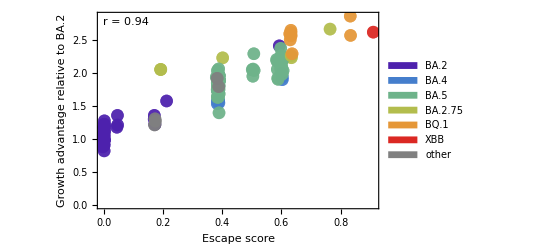

```mathematica
fig=ListPlot[Map[{#}&,escapeGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"Escape score","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[escapeGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/escape_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/escape_growth_advantage_correlation.png

```mathematica
bindingGAPairs=Table[{(pangoLineage/.pangoBindingMapping)+RandomVariate[NormalDistribution[0,0.002]],pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
bindingGACorr=Correlation[bindingGAPairs[[All,1]],bindingGAPairs[[All,2]]]
```

0.846939

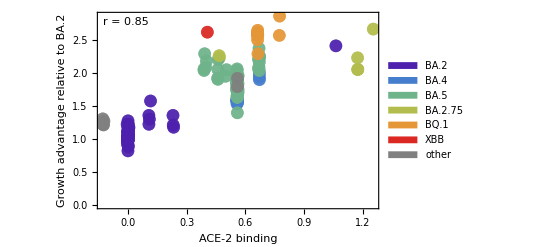

```mathematica
fig=ListPlot[Map[{#}&,bindingGAPairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"ACE-2 binding","Growth advantage relative to BA.2"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingGACorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/binding_growth_advantage_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/binding_growth_advantage_correlation.png

```mathematica
bindingEscapePairs=Table[{(pangoLineage/.pangoBindingMapping)+RandomVariate[NormalDistribution[0,0.005]],(pangoLineage/.pangoEscapeMapping)+RandomVariate[NormalDistribution[0,0.005]]},{pangoLineage,pangoLineages}];
```

```mathematica
bindingEscapeCorr=Correlation[bindingEscapePairs[[All,1]],bindingEscapePairs[[All,2]]]
```

0.803076

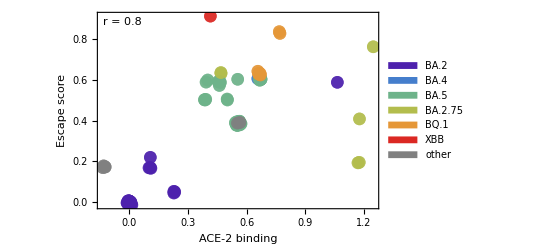

```mathematica
fig=ListPlot[Map[{#}&,bindingEscapePairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,pangoLineages/.pangoColorMapping],FrameLabel->{"ACE-2 binding","Escape score"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingEscapeCorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->legendPanel]
```

```mathematica
Export["figures/binding_escape_correlation.png",fig,"PNG",ImageResolution->300]
```

figures/binding_escape_correlation.png

```mathematica
gaColors=Table[colorRamp[((pangoLineage/.pangoGAMapping)-0.5)/2],{pangoLineage,pangoLineages}]
```

{RGBColor[0.88964606436784, 0.7338101820362201, 0.38274304551848004],RGBColor[0.91118609006272, 0.78576787149976, 0.50322565978784],RGBColor[0.9080997658087839, 0.778323206417122, 0.485962522785848],RGBColor[0.82402707320408, 0.67619500344089, 0.30985742567675995],RGBColor[0.8230159235680398, 0.675954004254695, 0.31062429536538005],RGBColor[0.82067264923748, 0.675395504121215, 0.31240146660906],RGBColor[0.7031304358619599, 0.6473802858415549, 0.4015470859696201],RGBColor[0.898615041622, 0.75544466574475, 0.432910387109],RGBColor[0.8299650248950399, 0.67761026531132, 0.30535400204688],RGBColor[0.8884853629089999, 0.731010400512625, 0.37625074378549994],RGBColor[0.894863114391256, 0.746394469022323, 0.411924246808532],RGBColor[0.88504927614412, 0.722722057145335, 0.35703123485113997],RGBColor[0.8802321737678799, 0.711102502325665, 0.3300871125128599],RGBColor[0.88567889051104, 0.72424077899932, 0.36055293839888003],RGBColor[0.90421441473364, 0.768951171885745, 0.46423008562358004],RGBColor[0.89591249937652, 0.748925738945785, 0.41779390769894],RGBColor[0.88802694953512, 0.72990464047021, 0.3736866409156399],RGBColor[0.895650343735696, 0.748293381233218, 0.41632755861471193],RGBColor[0.8913452335072, 0.7379088262876, 0.3922472282383999],RGBColor[0.8990655212214159, 0.756531288363853, 0.43543011297105205],RGBColor[0.8754507418479999, 0.699568989859, 0.3033425103559999],RGBColor[0.89748361172086, 0.7527154914955675, 0.42658181376917],RGBColor[0.08315402767867991, 0.12452710593223981, 0.15332800392937979],RGBColor[0.8974517462087199, 0.75263862722401, 0.42640357627484005],RGBColor[0.8853298961545599, 0.72339895361548, 0.35860086308431993],RGBColor[0.8597240354130798, 0.684703080322265, 0.28278436218726],RGBColor[0.89424455800912, 0.74490242064346, 0.40846439531864],RGBColor[0.7035228352566799, 0.6474738110048149, 0.40124948491146],RGBColor[0.8598591507936799, 0.68473528396019, 0.28268188883796],RGBColor[0.8592946204864398, 0.6846007328118949, 0.28311003633018006],RGBColor[0.8782348718427999, 0.70628471823115, 0.31891534508659997],RGBColor[0.8630646437234, 0.685499286794075, 0.28025079923729995],RGBColor[0.896948680990372, 0.7514251604080885, 0.423589716462734],RGBColor[0.7750980141337999, 0.664533165274775, 0.34696589207610007],RGBColor[0.753695477174, 0.65943204689825, 0.363197868303],RGBColor[0.8793316989649599, 0.7089304255211799, 0.3250503702231199],RGBColor[0.8919978495143199, 0.73948303145881, 0.39589758983803996],RGBColor[0.8825924286771999, 0.71679578205385, 0.3432890318533999],RGBColor[0.905843719078, 0.77288129204275, 0.47334348454100006],RGBColor[0.87516212500564, 0.698872803861745, 0.30172815240758],RGBColor[0.89040994812232, 0.73565278127281, 0.38701577541404],RGBColor[0.213270894484328, 0.40497818009150394, 0.5384307103635481],RGBColor[0.21390073936438397, 0.4061741868597119, 0.540020837450544],RGBColor[0.1528043162335041, 0.2810943406478722, 0.3704004320284643],RGBColor[0.15337210143692007, 0.2823706678685601, 0.37216999415522023],RGBColor[0.5115555088868479, 0.5994532848208639, 0.5455609457983681],RGBColor[0.8889290580993999, 0.732080658145825, 0.37873252153430004],RGBColor[0.89200614730228, 0.739503046935865, 0.39594400292966003],RGBColor[0.9208965888771841, 0.809738916093072, 0.5593228674756481],RGBColor[0.8208489509141599, 0.67543752417353, 0.31226775701052],RGBColor[0.50209400148038, 0.59688804525284, 0.5525616433203301],RGBColor[0.518871162628868, 0.601436732451224, 0.540147994476438],RGBColor[0.53682795396881, 0.60630524543558, 0.526861521271335],RGBColor[0.5484479944347139, 0.6094557146266519, 0.5182636958931991],RGBColor[0.261746674788944, 0.49702840257379194, 0.660814258704504],RGBColor[0.23200317951531202, 0.4405487473700159, 0.5857228528771921],RGBColor[0.508905336751328, 0.5987347601575039, 0.547521844068048],RGBColor[0.5009635709131399, 0.59658155865452, 0.5533980642129901],RGBColor[0.508810419871946, 0.5987090259352279, 0.5475920743531111],RGBColor[0.24972302613165798, 0.4741968044644439, 0.630458960090703],RGBColor[0.3122908697056819, 0.5454279044056759, 0.6929995521219873],RGBColor[0.30528291452090595, 0.5435278811685079, 0.6981848331124711],RGBColor[0.21879107876888002, 0.41546040829583997, 0.5523671490550801],RGBColor[0.3664579594265299, 0.56011389003854, 0.6529205885393552],RGBColor[0.275440638780092, 0.5230317474220559, 0.6953864903129221],RGBColor[0.21167985726123806, 0.40195697384288404, 0.5344139254932332],RGBColor[0.20181370576139002, 0.38322222764801994, 0.509505515119365],RGBColor[0.264580882891922, 0.5024102548059959, 0.6679695936408271],RGBColor[0.26735142447737, 0.5076712112616599, 0.674964193994295],RGBColor[0.277183411929482, 0.5263410836540758, 0.699786352690287],RGBColor[0.27986948196833, 0.53144163785094, 0.7065676934006552],RGBColor[0.30676872531386584, 0.5439307197937879, 0.6970854615758313],RGBColor[0.31001813279983986, 0.54481171140512, 0.6946811809514402],RGBColor[0.152961937763744, 0.28144865888019194, 0.370891676056304],RGBColor[0.301934036288336, 0.5426199206732479, 0.7006627134899761],RGBColor[0.276968291057474, 0.525932592568332, 0.6992432514658592],RGBColor[0.2108971188818361, 0.4004706389862481, 0.5324377984522262],RGBColor[0.268310677103408, 0.509492727430944, 0.677385954704328],RGBColor[0.24999931066055597, 0.4747214386672079, 0.631156477093746],RGBColor[0.34693937021521404, 0.5548219365256519, 0.6673626571499491],RGBColor[0.26350753110645797, 0.5003720767708438, 0.665259774442503],RGBColor[0.29274236783717594, 0.540127840860368, 0.7074637535129162],RGBColor[0.24313061634893, 0.46167853692173993, 0.613815545662755],RGBColor[0.16329279282368, 0.30467144004224, 0.40308886918688003],RGBColor[0.240299036249624, 0.45630167498203195, 0.6066668454708841],RGBColor[0.352918955033252, 0.556443144110936, 0.6629382813269821],RGBColor[0.257092918286444, 0.488191426278792, 0.6490652320707541],RGBColor[0.266763127083938, 0.5065540986414839, 0.6734789590576831],RGBColor[0.24269765274396798, 0.46085638623302394, 0.612722471514288],RGBColor[0.1294478188047201, 0.22859115234896016, 0.2976074585325203],RGBColor[0.17230801033157606, 0.32493679291956806, 0.43118573992331616],RGBColor[0.218826744533, 0.41552813369399993, 0.5524571920155],RGBColor[0.26440649607683003, 0.50207911325394, 0.6675293309554051],RGBColor[0.25442618284603996, 0.48312758637671993, 0.64233270412314],RGBColor[0.26442902182259004, 0.50212188718962, 0.6675862001935652],RGBColor[0.24614108841248, 0.46739509520064, 0.6214158823876801],RGBColor[0.25650640418121795, 0.4870776999285239, 0.647584499282163],RGBColor[0.09769036424323996, 0.1572034101663199, 0.1986320211733399],RGBColor[0.163627622677256, 0.305424105757808, 0.40413240153719604],RGBColor[0.26674401148579996, 0.5065178002043998, 0.6734306991903],RGBColor[0.26696567108123, 0.5069387076131399, 0.673990308290805],RGBColor[0.463353270884228, 0.586384512279704, 0.581226434778198],RGBColor[0.3540879595345399, 0.55676008901972, 0.6620733190578901],RGBColor[0.4482145197261259, 0.5822800369764679, 0.5924278018717412],RGBColor[0.24573709541942598, 0.4666279565458679, 0.620395948398291],RGBColor[0.3568859984172439, 0.5575187038731919, 0.6600030121785542],RGBColor[0.34298080952505194, 0.5537486766233359, 0.6702916498382822],RGBColor[0.36535360198137806, 0.559814472483404, 0.6537377175757231],RGBColor[0.25022341054511, 0.47514697991898, 0.6317222470283851],RGBColor[0.26029019761101196, 0.4942627111826159, 0.657137188547142],RGBColor[0.39519518312623386, 0.5679052344980119, 0.6316575273695192],RGBColor[0.20371947770996005, 0.38684108083128, 0.5143168896228602],RGBColor[0.3528573438885919, 0.5564264398650559, 0.6629838682476722],RGBColor[0.28220824880762, 0.53588270113116, 0.7124722210376702],RGBColor[0.21315041303027005, 0.40474939894386, 0.5381265389244452],RGBColor[0.239756009348018, 0.45527052609092394, 0.605295901905963],RGBColor[0.209988298897694, 0.3987448889062919, 0.530143361647629],RGBColor[0.309294335787356, 0.544615472829608, 0.6952167281675461],RGBColor[0.320621857253396, 0.5476866331663279, 0.6868353415606862],RGBColor[0.2989331270858239, 0.541806302853632, 0.7028831268675841],RGBColor[0.3842492935910299, 0.56493754364954, 0.6397565393401052],RGBColor[0.250628842683032, 0.4759168513529759, 0.632745814330212],RGBColor[0.4586038552545679, 0.585096832803824, 0.5847405917513882],RGBColor[0.415298274588194, 0.573355660465292, 0.6167829776243791],RGBColor[0.282812877366728, 0.537030824854704, 0.7139986861719481],RGBColor[0.6691814582905999, 0.639288826699175, 0.42729445404570005],RGBColor[0.17821661565007998, 0.33821877659743993, 0.44960052799928],RGBColor[0.235692364812914, 0.4475541080942519, 0.5950366913418991],RGBColor[0.21453962582850206, 0.407387362610436, 0.5416337912178572],RGBColor[0.25450208209494796, 0.48327171077666387, 0.642524321861718],RGBColor[0.350147257147178, 0.5556916709278039, 0.6649890981460231],RGBColor[0.334074248878094, 0.551333896313492, 0.6768817347340291],RGBColor[0.21826047231320003, 0.4144528444776, 0.5510275625562001],RGBColor[0.26510510705296997, 0.5034056993424599, 0.669293067188895],RGBColor[0.33095779645646595, 0.550488951980588, 0.6791876401049312],RGBColor[0.38744387608740793, 0.5658036709029439, 0.6373928244683281],RGBColor[0.26671960859456, 0.50647146177408, 0.6733690908489601],RGBColor[0.3207413292991279, 0.5477190248779039, 0.6867469425753482],RGBColor[0.25795615492118, 0.48983061854723997, 0.6512445876531301],RGBColor[0.273853293276446, 0.5200175513462278, 0.691379025678861],RGBColor[0.14976310925261604, 0.27425799614628804, 0.3609221915589561],RGBColor[0.14074808490836005, 0.25399307748248, 0.3328259228372601],RGBColor[0.37089217601176994, 0.5613161115608599, 0.6496396516096952],RGBColor[0.31660088179494794, 0.546596451136664, 0.6898105157817181],RGBColor[0.7786434243425598, 0.66537818459198, 0.34427700457032],RGBColor[0.82908516743912, 0.67740055853471, 0.30602129795363997],RGBColor[0.7489187357379199, 0.65829354992636, 0.36682061422224005],RGBColor[0.271678213523012, 0.515887311998616, 0.6858877478391422],RGBColor[0.14082886594260793, 0.25417466557654383, 0.3330776854015278],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.05, 0.05, 0.05],RGBColor[0.129513185380496, 0.22873809020412797, 0.297811180320536],RGBColor[0.31713779166862993, 0.54674202016634, 0.6894132488917052],RGBColor[0.25547894860274, 0.48512667378731994, 0.6449905511565901],RGBColor[0.05, 0.05, 0.05]}

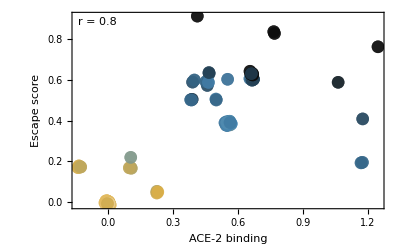

```mathematica
fig=ListPlot[Map[{#}&,bindingEscapePairs],PlotTheme->"FullAxes",Frame->{True,True,False,False},PlotMarkers->{"•",Medium},PlotStyle->Map[Directive[Opacity[0.75],#]&,gaColors],FrameLabel->{"ACE-2 binding","Escape score"},Epilog->{Directive[FontSize->11,FontFamily->"Helvetica"],Text["r = "<>ToString[Round[bindingEscapeCorr,0.01]],Scaled[{0.02,0.95}],{-1,0}]},PlotLegends->gaPanel]
```

```mathematica
Export["figures/binding_escape_correlation_ramp.png",fig,"PNG",ImageResolution->300]
```

figures/binding_escape_correlation_ramp.png

## Multiple regression

Predict continuous variable growth advantage Y from escape X_1 and binding X_2

```mathematica
regressionData=Table[{pangoLineage/.pangoEscapeMapping,pangoLineage/.pangoBindingMapping,pangoLineage/.pangoGAMapping},{pangoLineage,pangoLineages}];
```

```mathematica
lm=LinearModelFit[regressionData,{x1,x2},{x1,x2}]
```

FittedModel[1.02905+1.516 x1+0.412183 x2]

```mathematica
lm["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 1.02905 | 0.0204809 | 50.2441 | 1.7512×10^-99
x1 | 1.516 | 0.0833273 | 18.1933 | 1.05958×10^-40
x2 | 0.412183 | 0.063815 | 6.45903 | 1.2224×10^-9